## Lab07

## Problem 1 : sum of positive num

```mathematica
ListN = {1,2,-5,8,10,22,-5,-9,28}
```

```mathematica
PosN[numList_]:= Module[
{Sum = 0,i},
For[i=1,i <= Length[numList], i++,
 Sum = Sum + If[numList[[i]] >0, numList[[i]],0]];
Sum]
```

```mathematica
PosN[ListN]
```

```mathematica
For[i=1, i<=6,i++,
Print[i];
If[i>2, {Print["not OK"]; Break[]}, Print["Ok"]]]
```

## Problem 2

```mathematica
List1 = {1,0,15}
```

```mathematica
List2 = {2,2,10,1}
```

```mathematica
SumNon0[list_] := Module[
{Sum = 0, i},
For[i=1,i <= Length[list], i++, 
Sum = Sum + If[list[[i]] != 0,(1./ list[[i]]),{Print["Infinity"]; Break[]}]];
Sum
]
```

```mathematica
SumNon0[List1]
```

```mathematica
SumNon0[List2]
```

## Problem 3

```mathematica
Clear[LP]
```

```mathematica
PrN1N2[N1_, N2_]:=
Module[
{i, list= {}, plot, LP},
For[i = N1, i <= N2, i++, 
If[PrimeQ[i], list= Join[list, {i}]]];
plot = ListPlot[list, PlotStyle->{Red, PointSize[0.015]}];
{list,plot}
]
```

```mathematica
LP = PrN1N2[10,201];
```

```mathematica
LP[[1]]
```

{11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199}

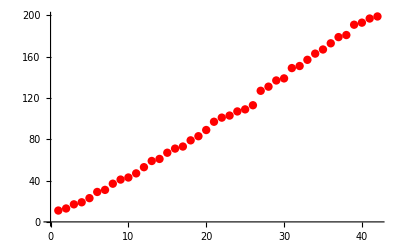

```mathematica
LP[[2]]
```

## Problem 4

```mathematica
primeNum[N_]:=Module[
{primeList = {1}, i},
	For[i = 1,i<= N, i++,
 If[PrimeQ[i],primeList = Join[primeList, {i}]]];
 Length[primeList]]
```

```mathematica
LN = Table[{i,primeNum[i]}, {i,1,100}]
```

{{1,1},{2,2},{3,3},{4,3},{5,4},{6,4},{7,5},{8,5},{9,5},{10,5},{11,6},{12,6},{13,7},{14,7},{15,7},{16,7},{17,8},{18,8},{19,9},{20,9},{21,9},{22,9},{23,10},{24,10},{25,10},{26,10},{27,10},{28,10},{29,11},{30,11},{31,12},{32,12},{33,12},{34,12},{35,12},{36,12},{37,13},{38,13},{39,13},{40,13},{41,14},{42,14},{43,15},{44,15},{45,15},{46,15},{47,16},{48,16},{49,16},{50,16},{51,16},{52,16},{53,17},{54,17},{55,17},{56,17},{57,17},{58,17},{59,18},{60,18},{61,19},{62,19},{63,19},{64,19},{65,19},{66,19},{67,20},{68,20},{69,20},{70,20},{71,21},{72,21},{73,22},{74,22},{75,22},{76,22},{77,22},{78,22},{79,23},{80,23},{81,23},{82,23},{83,24},{84,24},{85,24},{86,24},{87,24},{88,24},{89,25},{90,25},{91,25},{92,25},{93,25},{94,25},{95,25},{96,25},{97,26},{98,26},{99,26},{100,26}}

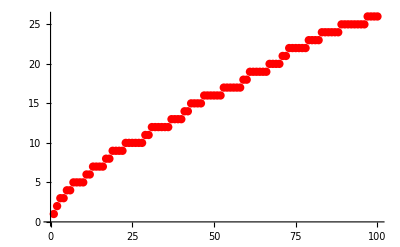

```mathematica
GfN = ListPlot[LN, PlotStyle->{Red, PointSize[0.015]}]
```

```mathematica
InT = LN[[{1,25,50,75,100}]]
```

{{1,1},{25,10},{50,16},{75,22},{100,26}}

```mathematica
fQint = Interpolation[InT, Method->"Spline"]
```

InterpolatingFunction[…]

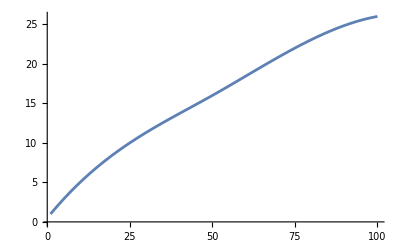

-Graphics-

```mathematica
GF = Plot[fQint[t], {t,1,Length[LN]}]
```

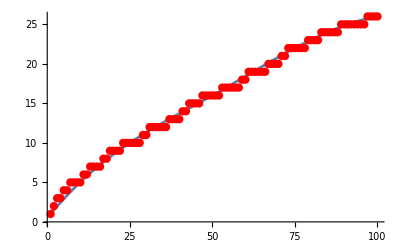

-Graphics-

```mathematica
Show[{GF, GfN}]
```

```mathematica
squaredError[func_, data_] := Module[
{error , i},
error = Sqrt[Sum[(func[i] - data[[i]][[2]])^2 , {i,1, 100}]];
error
]
```

```mathematica
Sqrt[Sum[(fQint[i] - LN[[i]][[2]])^2 , {i,1, 100}]]
```

4.55751

```mathematica
squaredError[fQint, LN]
```

4.55751

## Problem 5 - conditional if composed function

```mathematica
Clear[f1]
```

```mathematica
R1 = 3
```

3

```mathematica
f1[t_] := {R1 * Cos[t], R1 Sin[t] + R1}
```

```mathematica
f2[t_] := {t, R1}
```

```mathematica
Tr1[t_] := If[t>= 0 && t<= 2Pi, f1[t], f2[t]]
```

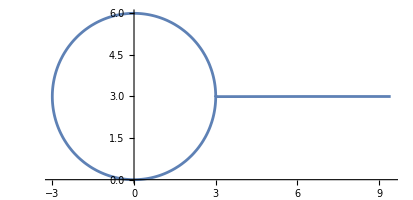

```mathematica
ParametricPlot[Tr1[t], {t,0,3Pi}, Exclusions->None]
```

#### evaluate each test and return the value where test is true [test, value, test, value]

```mathematica
F[x_]:= Which[x > 0, 1,x<0, 2, x== 0, 3]
```

```mathematica
F[1]
```

1

```mathematica
F[-2]
```

2

```mathematica
F[0]
```

3

```mathematica
F[x_]:= Which[x <0, f1[x], x<=5 && x>= 0, f1[x], x > 5, f1[x]]
```

```mathematica
F[1]
```

{3 Cos[1],3+3 Sin[1]}

## Problem 5.2

```mathematica
Clear[t,f1,f2,f3,Tra5, disk]
```

```mathematica
R1 = 3;
```

```mathematica
f1[t_] := {R1 Cos[t], R1 Sin[t] + R1}
```

```mathematica
f2[t_] := {t, R1}
```

```mathematica
f3[t_]:= {R1 Cos[t] + R1 + 3Pi, R1 Sin[t] + R1}
```

```mathematica
Tra5[t_] := Which[t >= 0 && t <= 2Pi, f1[t], t>2Pi && t < 3Pi, f2[t], t>= 3Pi, f3[t]]
```

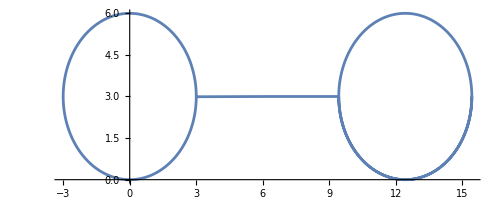

```mathematica
plot = ParametricPlot[Tra5[t], {t,0,6Pi}, Exclusions->None]
```

```mathematica
RD = 1/2;
```

```mathematica
disk[t_] := {Red, Disk[Tra5[t], RD]}
```

```mathematica
showBoth[t_]:= Show[{plot,Graphics[disk[t]]}]
```

```mathematica
Manipulate[showBoth[t], {t,0,5Pi}]
```

## Problem 6

```mathematica
Ladder = {{1,1}, {5,5},{9,9}, {13,13}, {17,17}, {21,21}, {24,21},{28,17}, {32,13}, {36,9}, {40,5}};
```

```mathematica
MatrixForm[Ladder]
```

(1 | 1
5 | 5
9 | 9
13 | 13
17 | 17
21 | 21
24 | 21
28 | 17
32 | 13
36 | 9
40 | 5)

```mathematica
ladderTranspose = Transpose[Ladder]
```

{{1,5,9,13,17,21,24,28,32,36,40},{1,5,9,13,17,21,21,17,13,9,5}}

```mathematica
tMax = Max[ladderTranspose[[1]]]
```

40

```mathematica
fLadder = Interpolation[Ladder, InterpolationOrder->0]
```

InterpolatingFunction[…]

```mathematica
fL5[t_]:= {t, fLadder[t]}
```

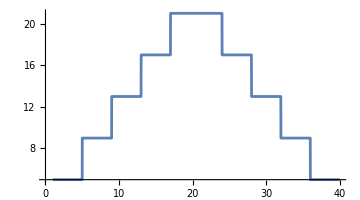

```mathematica
Tra6 = ParametricPlot[fL5[t], {t,1,tMax}, ImageSize->Medium]
```

```mathematica
RR5 = 3
```

3

```mathematica
ObjectPol[s_]:= {Red, RegularPolygon[fL5[s], RR5, 3]}
```

```mathematica
showBoth[t_] := Show[{Tra6, Graphics[ObjectPol[t]]}, PlotRange -> {{0,tMax}, {-10,30}}, AxesOrigin -> {0,0}]
```

```mathematica
Manipulate[showBoth[t], {t, 1, tMax}]
```

## Problem 7

```mathematica
Clear[GPNew, GGPNew]
```

```mathematica
RR5 = 5; nreg = 3;
```

```mathematica
newObject = {Red, RegularPolygon[{0,0}, RR5, nreg]}
```

{RGBColor[1, 0, 0],RegularPolygon[{0,0},5,3]}

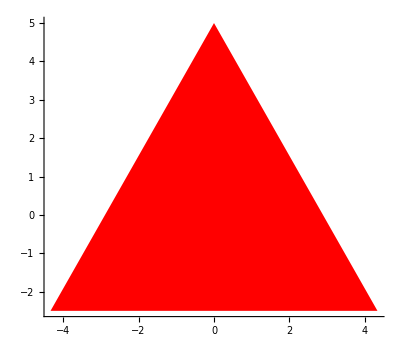

```mathematica
Graphics[newObject, Axes->True]
```

```mathematica
objectRotate[a_,s_] := GeometricTransformation[newObject, Composition[TranslationTransform[fL5[s]], RotationTransform[a]]]
```

```mathematica
GPNew[a_,s_] := Graphics[objectRotate[a,s], PlotRange->{{0,40}, {-10,30}}, Axes->True]
```

```mathematica
GGPNew[a_,s_] := Show[GPNew[a,s], Tra6]
```

```mathematica
Manipulate[GGPNew[s,s], {s,1,tMax}]
```